```mathematica
relErrorMthElt[backorbit_,m_,fx_,precision_]:=
Module[{j,k,el,z,,loglinpairs,loglinpair,la,arg,args,nm,aa,xx,b1,m1,bb,zeros,zr,approxr,estimate,fxerror,relerror,relerrors,rellog,relerrmoduli},
zeros=backorbit;
el=Length[zeros];
args={};
loglinpairs={};

k=1;
z=zeros[[k]];
la=Re[Log[Abs[z-fx]]];
arg=Arg[z-fx];
loglinpair={arg,la};
args=Append[args,arg];
loglinpairs=Append[loglinpairs,loglinpair];

For[k=1,k<el,k++;
z=zeros[[k]];
la=Re[Log[Abs[z-fx]]];
arg=Arg[z-fx];
While[Not[arg>Max[args]],arg=arg+2*Pi];
args=Append[args,arg];
loglinpair={arg,la};
loglinpairs=Append[loglinpairs,loglinpair]];

outargs=args;
outpairs=loglinpairs;
nm=FindFit[loglinpairs,aa*xx+bb,{aa,bb},{xx},PrecisionGoal->precision];
m1=nm[[1,2]];
b1=nm[[2,2]];

relerrors={};
relerrmoduli={};
j=m;
zr=zeros[[j]];
arg=args[[j]];
approxr=Exp[m1*arg+b1];
estimate=approxr*(Cos[arg]+I*Sin[arg]);
fxerror=zr-fx-estimate;
relerror=Abs[fxerror/(zr-fx)];

Return[relerror]]
```

```mathematica
absErrorMthElt2[backorbit_,m_,fx_,precision_]:=
Module[{j,k,el,z,,loglinpairs,loglinpair,la,arg,args,nm,aa,xx,b1,m1,bb,zeros,zr,approxr,estimate,fxerror,relerror,relerrors,rellog,relerrmoduli},
zeros=backorbit;
el=Length[zeros];
args={};
loglinpairs={};

(* omit k = 1 *)
For[k=1,k<el,k++;
z=zeros[[k]];
la=Re[Log[Abs[z-fx]]];
arg=Arg[z-fx];
While[Not[arg>Max[args]],arg=arg+2*Pi];
args=Append[args,arg];
loglinpair={arg,la};
loglinpairs=Append[loglinpairs,loglinpair]];

outargs=args;
outpairs=loglinpairs;
nm=FindFit[loglinpairs,aa*xx+bb,{aa,bb},{xx},PrecisionGoal->precision];
m1=nm[[1,2]];
b1=nm[[2,2]];

relerrors={};
relerrmoduli={};
j=m;
zr=zeros[[j]];
arg=args[[j]];
approxr=Exp[m1*arg+b1];
estimate=approxr*(Cos[arg]+I*Sin[arg]);
fxerror=zr-fx-estimate;
abserror=Abs[fxerror];

Return[abserror]]
```

```mathematica
stream=OpenRead["cplxfixedpoints17april16no2"];
ls=ReadList[stream];
Close[stream]
```

cplxfixedpoints17april16no2

## Code for data file “cplxfxNrhoNrun20may16no1” from notebook “make ‘cplxfxNrhoNrun20may16no1’#1.nb”; followup notebooks #2, #3, #4, #5 use Open Append and bring n up to 600.

```mathematica
streamzeros=OpenRead["betterbarryzeros"];
betterbarryzeroslist=ReadList[streamzeros];
Close[streamzeros];
streamfx=OpenRead["cplxfixedpoints17april16no2"];
fxlist=ReadList[streamfx];
Close[streamfx];

stream1=OpenWrite["cplxfxNrhoNrun20may16no1"];
stream2=OpenWrite["cplxfxNrhoNloglinear20may16no1"];
stream3=OpenWrite["relativeerrorsfxNrhoN20may16no1"];
stream4=OpenWrite["loglinearparameters20may16no1"];
stream5=OpenWrite["errorsfxNrhoN20may20no1"];
precision=500;
errors={};
abserrors={};
relativeerrors={}; 
absrelerrors={};
errors0={};
errors1={};
errors2={};
relativeerrors0={};
relativeerrors1={};
relativeerrors2={};
For[n=0,n<50,n++;
orbit={};
shortorbit={};
data={};
orbitpairs={};
args={};
thetaset={};
errorpairs={};
relerrorpairs={};
nearbyzero=1/2+I*Im[betterbarryzeroslist[[n]]];
fx=N[fxlist[[n,2]],1000];
Print["&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&"];
Print["fixed point ~ ",N[Round[fx,1/10^10]]];

k=1;
zr=nearbyzero;
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
arg=Arg[zr-fx];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
datum={arg,la};
Write[stream2,{n,k,arg,la}];
data=Append[data,datum];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair];


For[k=1,k<100,k++;
startcenter=fx;
x=orbit[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision+50,WorkingPrecision->precision+100][[1,2]];
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
shortorbit=Append[shortorbit,zr];
arg=Arg[zr-fx];
While[Not[arg>Last[args]],arg=arg+2*Pi];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
datum={arg,la};
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair];
Write[stream2,{n,k,arg,la}];
data=Append[data,datum];
];(*close k loop *)


Print["log r vs theta"];
Print[ListPlot[data]];

shortdata=Drop[data,1];

nm=FindFit[shortdata,aa*xx+bb,{aa,bb},{xx},PrecisionGoal->precision];
m=nm[[1,2]];
b=nm[[2,2]];
Write[stream4,{n,m,b}];
Print["loglinear parameters"];
Print["slope ~ ",N[Round[m,1/10^5]]];
Print["intercept ~ ",N[Round[b,1/10^5]]];

u=1;
zr=orbit[[u]];
theta=args[[u]];
la=data[[u,1]];
estimatedlogr=m*theta+b;
estimatedr=E^estimatedlogr;
estimatedzrminusfx=estimatedr*E^(I*theta);

error=zr-fx-estimatedzrminusfx;
errortheta=Arg[error];
errorla=Re[Log[Abs[error]]];
errorpair={errorla*Cos[errortheta],errorla*Sin[errortheta]};
errorpairs=Append[errorpairs,errorpair];


For[u=1,u<Length[orbit],u++;
zr=orbit[[u]];
theta=args[[u]];
While[Not[theta>Max[thetaset]],theta=2*Pi+theta];
thetaset=Append[thetaset,theta];
la=Re[Log[Abs[zr-fx]]];
estimatedlogr=m*theta+b;
estimatedr=E^estimatedlogr;
estimatedzrminusfx=estimatedr*E^(I*theta);

error=zr-fx-estimatedzrminusfx;
errortheta=Arg[error];
errorla=Re[Log[Abs[error]]];
errorpair={errorla*Cos[errortheta],errorla*Sin[errortheta]};
errorpairs=Append[errorpairs,errorpair]
]; (* close u-loop  *)

Print["lg xfrm orbit for zero   ",n];
jplot=ListPlot[orbitpairs,Joined->True,PlotStyle->Blue];
rplot=ListPlot[orbitpairs,PlotStyle->{Red,PointSize[.01]}];
Print[Show[jplot,rplot]];


Print["lg xfrm errors for zero   ",n];
jplot=ListPlot[errorpairs,Joined->True,PlotStyle->Blue];
rplot=ListPlot[errorpairs,PlotStyle->{Red,PointSize[.01]}];
Print[Show[jplot,rplot]];



zr=nearbyzero;
theta=Arg[zr-fx];
la=Re[Log[Abs[zr-fx]]];
estimatedlogr=m*theta+b;
estimatedr=E^estimatedlogr;
estimatedzrminusfx=estimatedr*E^(I*theta);
error=zr-fx-estimatedzrminusfx;
errortheta=Arg[error];
errorla=Re[Log[Abs[error]]];
abserror=Abs[error];
relerror=error/(zr-fx);
relerrortheta=Arg[relerror];
relerrorla=Re[Log[Abs[relerror]]];
absrelerror=Abs[relerror];
abserrors=Append[abserrors,abserror];
absrelerrors=Append[absrelerrors,absrelerror];
Write[stream5,{n,error}];
errors=Append[errors,{Im[fx],error}];
Write[stream3,{n,relerror}];
relativeerrors=Append[relativeerrors,{Im[fx],relerror}]

];(* close n loop *)

Close[stream1];  
Close[stream2];
Close[stream3]; 
Close[stream4];
Close[stream5];

Print["|relative spiral errors| over all rho"];
Print[ListPlot[absrelerrors,PlotStyle->Red]];
Print["|spiralerrors| over all rho"];
Print[ListPlot[abserrors,PlotStyle->Blue]]
```

```mathematica
stream1=OpenRead["cplxfxNrhoNrun20may16no1"];
list=ReadList[stream1];
Close[stream1]
```

cplxfxNrhoNrun20may16no1

```mathematica
list[[1]]
```

{1,1,1/2+14.13472514173469379045725198356247027078425711569924317568556746014996342980925676494901039317156101277920297154879743676614269146988225458250536323944713778041338123720597054962195586586020055556672583601077370020541098266150754278051744259130625448197865107230493872562973832157742039521572567480933214003499046803434626731442092037738548714137831735639699536542811307968053149168852906782082298049264338666734623320078758761792005604868054356801444424651065597568665903228686510544859444320624072727032094274522213048748720924123851418351460542790152447833835425453344004487936806761697300819000731393854983736215013045167269683892003917628512321285422052396913342583227533516406016976352756375896953767492033612720925999173042707568308795118445348918008630082648312516911271068291052375961797743181517071354531677549515382893784903647470972701994848553220925357435790922612524773659551801697523346121397731600535412592674745572587780147260983080897860071253208750939599796666067537838121489190886 ⅈ}

```mathematica
list[[2]]
```

{1,2,-2.18529099944874669374623200835864370359494162598614017788542516818606187329070184503934450681276740976187968761193593764056712472838075916984820489148543298576460377920784435335408855514510422923721800307470296735027830875424711456433183911255968619533107166400970833575505528534815574236657844855361022354706115196631068010176048458953155539681726198045435464327944632833789508942855947119894623844476570050480965974545586662957492512228481614544303335716814869987992258045039243278913408094825820125184525797118503400098152256687216156314394925753820211360628179842375035515558870136219959378737906+16.4107245489643803769875190889758405663367642968252531164541522361646428770755165929599837007032287335091556920789666777788468352595968826787655224544461070362652915955143394919968033931688706461274120505818098544095919790996258900037169915607009858188121351573659361760857292461617310630122787725600025505822036428361717572557001117167842579308634603872336954859841634208493397307884816878629099817558516955542872375545653557112927266094718046811975439183592655108691214657480338760033306718267137728641186559214256269068387283622537726710378236834931071805361155740354821248441633407922556109963944 ⅈ}

```mathematica
Last[list][[1]]
```

600

```mathematica
ls[[1]]
```

{1,-2.385935683424245430398183275744593036220109314963887335157493204832347633523596058249474253833629533884780524961593840844747475905794850465385441687344375276090258424428452222988188671578573887441370253512254841440654281865567205558503458420120956952863419189113438129546883345240085069026066275291455919528070561343000118682969413570660837996892963089829005841411957056105587064326824189229779797715358481106657206349693597386713288829393906062669652387454304102497363533825726278798018091965014575218811831108602731219699502534827142260232481469476004087007791983040841109358181076919622881158503076005219095833280493932263203585991540880899807923031370327018679873370608321687162499880488126344319056020746014071754732321354037869158544053338129579479376673281853873136095363767350818656510341374362923873521487901593631883596222901947360079516674565924020208847471131462286772285159745085751641419697753594058550456928226255140988622129706391686146542801754188435778597068543829521576520663912075+16.27098706219679017233151174242644803888699932850806142230398747453124608174527735115146697662857737397621682692028084896636886032090787700033832793082915074606704010514346554030469527511515425330624120998636361089706826134148690952795851469919890279710150893474324435358676863934909398406118654047404322317267371891675200516440805049274277141173085814134309337853440520410096393947924718391174516914936641688327492377899052851877755493080468520467912973841246584688402785877023905785795567027609493133498347309721741423311541039151995088659956801720354967389888879183732302359896835395803256607771490660654298127167774077033124520891105811882204946298512526417624675440744179204377073280160849286196982365315895279670106370263813926413188484346017134768175831471686005455622301837491821763023988675778238994251345453310489690381172903231974104596389822506772231598552942699302737929320710770924496206068589691400957402440216999277932123970516957405903101158622152506436249693401240887965621257921089 ⅈ}

```mathematica
list[[1,1]]
```

1

```mathematica
precision=500;
data={};
m=1;
For[n=0,n<1,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)
Print["length backorbit  ",Length[backorbit]];
datum = relErrorNthElt[backorbit,m,fx,precision];
Print[n];
Print[datum]
] (* close n loop *)
```

length backorbit  100

1

0.3446579975915104005586525273212161506254234508960398504134699673427336741630032675697769321953108204685005365557403468058704107610300819295606604376561154278654352329053711404831806476588612247223977314213455614789503355147883346543100819172908544888698500550957356679705300423886923819156868108280171934195533289279057588769625460704647588875780675962489517813983772158268357775719569552521072326649066265738639982218277021841346428443910855173312756259611539733060500825152944436

$Aborted

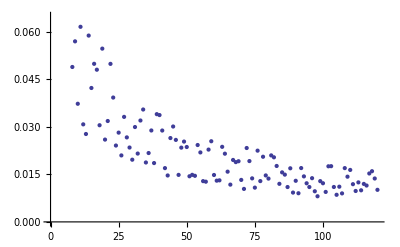

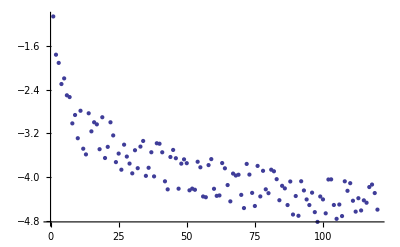

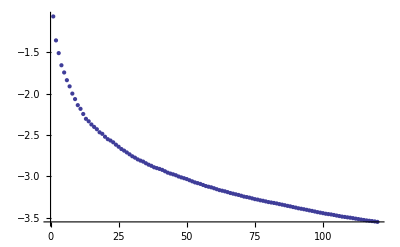

```mathematica
precision=500;
data={};
logdata={};
logmeandata={};
m=1;
For[n=0,n<600,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)


datum = relErrorMthElt[backorbit,m,fx,precision];
data=Append[data,datum];
logmeandata=Append[logmeandata,Log[Mean[data]]];
logdata=Append[logdata,Log[datum]]
] (* close n loop *);
Print[ListPlot[data]];
Print[ListPlot[logdata]];
Print[ListPlot[logmeandata]]
```

```mathematica
precision=500;
data={};
logdata={};
logmeandata={};
m=1;
For[n=0,n<600,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)


datum = relErrorMthElt[backorbit,m,fx,precision];
data=Append[data,datum];
logmeandata=Append[logmeandata,Log[Mean[data]]];
logdata=Append[logdata,Log[datum]]
] (* close n loop *);
Print["relative error"];
Print[ListPlot[data]];
Print["log relative error"];
Print[ListPlot[logdata]];
Print["running mean of log relative error"];
Print[ListPlot[logmeandata]]
```

### leaf 6.5left

relative error

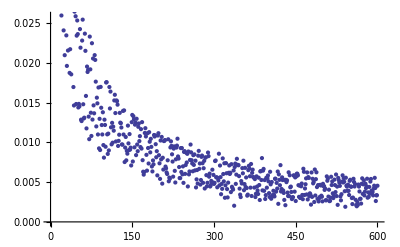

log relative error

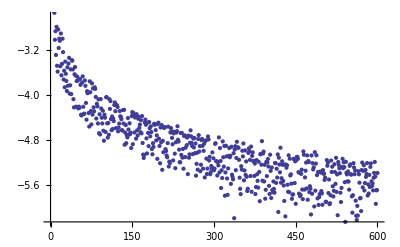

running mean of log relative error

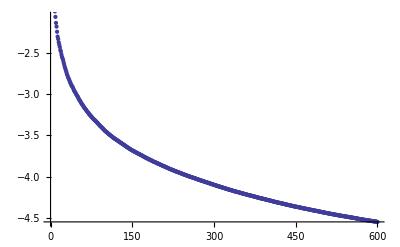

relative error

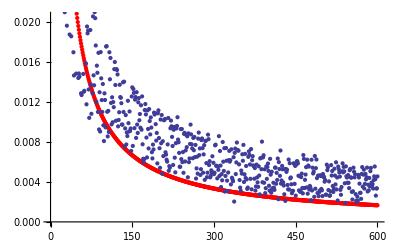

log relative error

-Graphics-

running mean of log relative error

-Graphics-

```mathematica
precision=500;
data={};
logdata={};
logmeandata={};
redcurve={};
m=1;
For[n=0,n<600,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)


datum = relErrorMthElt[backorbit,m,fx,precision];
data=Append[data,datum];
redcurve=Append[redcurve,N[1/n]];
logmeandata=Append[logmeandata,Log[Mean[data]]];
logdata=Append[logdata,Log[datum]]
] (* close n loop *);
Print["relative error"];
Print[Show[ListPlot[redcurve,PlotStyle->Red],ListPlot[data]]];
Print["log relative error"];
Print[ListPlot[logdata]];
Print["running mean of log relative error"];
Print[ListPlot[logmeandata]]
```

relative error

-Graphics-

log relative error

-Graphics-

running mean of log relative error

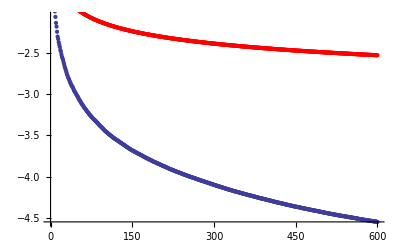

```mathematica
precision=500;
data={};
logdata={};
logmeandata={};
redcurve={};
m=1;
For[n=0,n<600,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)


datum = relErrorMthElt[backorbit,m,fx,precision];
data=Append[data,datum];
redcurve=Append[redcurve,N[-Log[n]^.5]];
logmeandata=Append[logmeandata,Log[Mean[data]]];
logdata=Append[logdata,Log[datum]]
] (* close n loop *);
Print["relative error"];
Print[ListPlot[data]];
Print["log relative error"];
Print[ListPlot[logdata]];
Print["running mean of log relative error"];
Print[Show[ListPlot[logmeandata],ListPlot[redcurve,PlotStyle->Red]]]
```

relative error

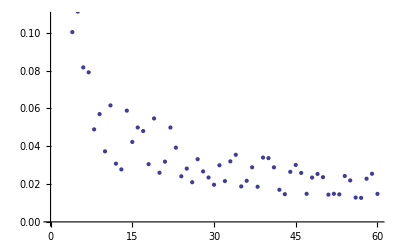

log relative error

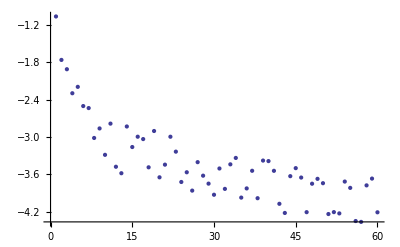

running mean of log relative error

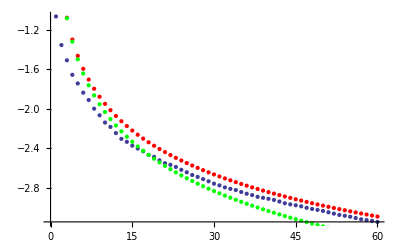

running mean of log relative error

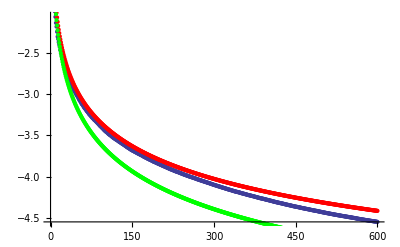

```mathematica
precision=500;
data={};
logdata={};
logmeandata={};
redcurve={};
greencurve={};
m=1;
For[n=0,n<60,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)


datum = relErrorMthElt[backorbit,m,fx,precision];
data=Append[data,datum];
redcurve=Append[redcurve,N[-Log[n]^.8]];
greencurve=Append[greencurve,N[-Log[n]^.85]];
logmeandata=Append[logmeandata,Log[Mean[data]]];
logdata=Append[logdata,Log[datum]]
] (* close n loop *);
Print["relative error"];
Print[ListPlot[data]];
Print["log relative error"];
Print[ListPlot[logdata]];
Print["running mean of log relative error"];
Print[Show[ListPlot[logmeandata],ListPlot[redcurve,PlotStyle->Red],ListPlot[greencurve,PlotStyle->Green]]]
```

cplxfxNrhoNrun20may16no1

relative error

-Graphics-

log relative error

-Graphics-

running mean of log relative error

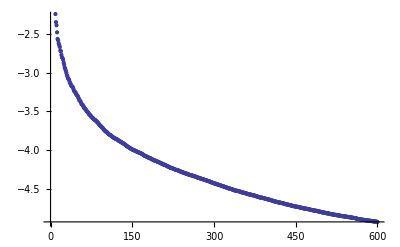

log running mean data

-Graphics-

```mathematica
stream1=OpenRead["cplxfxNrhoNrun20may16no1"];
list=ReadList[stream1];
Close[stream1]
precision=500;
data={};
logdata={};
logmeandata={};
meanlogdata={};
redcurve={};
greencurve={};
m=1;
For[n=0,n<600,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)


datum = relErrorMthElt[backorbit,m,fx,precision];
data=Append[data,datum];
logdata=Append[logdata,Log[datum]];
meanlogdata=Append[meanlogdata,Mean[logdata]];
logmeandata=Append[logmeandata,Log[Mean[data]]]
] (* close n loop *);
Print["relative error"];
Print[ListPlot[data]];
Print["log relative error"];
Print[ListPlot[logdata]];
Print["running mean of log relative error"];
Print[Show[ListPlot[meanlogdata]]];
Print["log running mean data"];
Print[Show[ListPlot[logmeandata]]]
```

```mathematica
stream1=OpenRead["cplxfxNrhoNrun20may16no1"];
list=ReadList[stream1];
Close[stream1]
precision=500;
data={};
logdata={};
logmeandata={};
redcurve={};
greencurve={};
m=1;
For[n=0,n<600,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)


datum = relErrorMthElt[backorbit,m,fx,precision];
data=Append[data,datum];
redcurve=Append[redcurve,N[-Log[n]^.8]];
greencurve=Append[greencurve,N[-Log[n]^.85]];
logdata=Append[logdata,Log[datum]];
logmeandata=Append[logmeandata,Log[Mean[data]]]
] (* close n loop *);
Print["relative error"];
Print[ListPlot[data]];
Print["log relative error"];
Print[ListPlot[logdata]];
Print["log running mean relative error"];
Print[Show[ListPlot[logmeandata],ListPlot[redcurve,PlotStyle->Red],ListPlot[greencurve,PlotStyle->Green]]]
```

cplxfxNrhoNrun20may16no1

relative error

-Graphics-

## leaf6point5left

log relative error

-Graphics-

### leaf6point5right

log running mean relative error

-Graphics-

```mathematica
absErrorMthElt2[backorbit_,m_,fx_,precision_]
```

cplxfxNrhoNrun20may16no1

absolute error

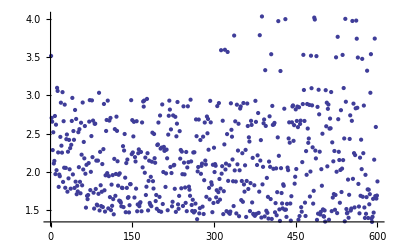

log relative error

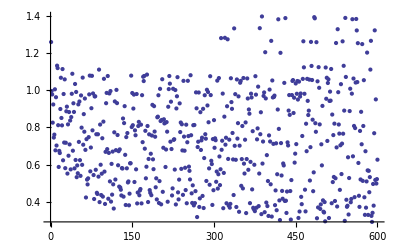

log running mean absolute error

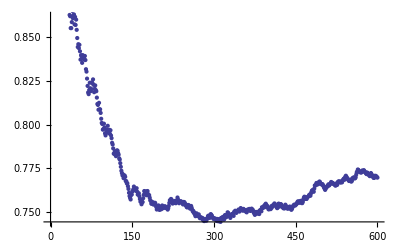

```mathematica
stream=OpenRead["cplxfixedpoints17april16no2"];
ls=ReadList[stream];
Close[stream];
stream1=OpenRead["cplxfxNrhoNrun20may16no1"];
list=ReadList[stream1];
Close[stream1]
precision=500;
data={};
logdata={};
logmeandata={};
redcurve={};
greencurve={};
m=1;
For[n=0,n<600,n++;

backorbit={};
fx=ls[[n,2]];

For[a=0,j=a<Length[list],a++;

If[
list[[a,1]]==n,backorbit=
Append[
backorbit,list[[a,3]]
] (* close Append  *)

] (*close If loop  *)

]; (*close a loop *)


datum = absErrorMthElt2[backorbit,m,fx,precision];
data=Append[data,datum];
redcurve=Append[redcurve,N[-Log[n]^.8]];
greencurve=Append[greencurve,N[-Log[n]^.85]];
logdata=Append[logdata,Log[datum]];
logmeandata=Append[logmeandata,Log[Mean[data]]]
] (* close n loop *);
Print["absolute error"];
Print[ListPlot[data]];
Print["log relative error"];
Print[ListPlot[logdata]];
Print["log running mean absolute error"];
Print[ListPlot[logmeandata]]
(*
Print[Show[ListPlot[logmeandata],ListPlot[redcurve,PlotStyle->Red],ListPlot[greencurve,PlotStyle->Green]]]
*)
```